```mathematica
Quit[]
```

```mathematica
<<pkg`
```

```mathematica
m1=1.5;m2=1; λi=0;λf=2; (*G=1;*) (*ϵ*)


Rinit={1,.5,1.5};
Pinit=(*p*)(-.1) *{1,-4,-1};  (*-0.23177026220258928<p<0.23233759931552855 will make energy negative*)
S1init={1,1,1.9};
S2init={0,0,1}-Cross[Rinit,Pinit]-S1init;
```

```mathematica
NmHflow[5/2,1,2{ 1,1,1},1{1/2,-1/2,1/3},{0,1,1} .054,{1,-3/10,0}.054,1000,0 ]
```

{{{-3.98368,-1.01441,-3.52475}},{{-0.136588,0.465284,-0.0282498}},{{0.0141221,0.0402432,0.0633486}},{{0.0378913,-0.0380083,-0.0172645}}}

```mathematica
SeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
NmSeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
```

{{-0.0898791,1.56465,1.02166},{-0.161073,-0.0976947,0.380146},{-1.10525,1.51582,1.44593},{0.410646,-1.38542,-0.706732}}

{{-0.089879,1.56465,1.02166},{-0.161073,-0.0976947,0.380146},{-1.10525,1.51582,1.44593},{0.410646,-1.38542,-0.706732}}

```mathematica
Jsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
NmJsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
Lsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
 NmLsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
Jzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
NmJzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
```

{{-0.275242,-1.08362,1.5},{-0.368085,0.185777,-0.1},{0.103159,-1.41045,1.9},{0.0671445,1.9901,-0.45}}

{{-0.275242,-1.08362,1.5},{-0.368085,0.185777,-0.1},{0.103159,-1.41045,1.9},{0.0671446,1.9901,-0.45}}

{{-0.889884,-0.712424,-1.48343},{-0.133993,0.398411,0.0575699},{1.,1.,1.9},{-1.55,-1.25,-0.45}}

{{-0.889884,-0.712424,-1.48343},{-0.133993,0.398411,0.0575699},{1.,1.,1.9},{-1.55,-1.25,-0.45}}

{{-0.870796,0.701224,1.5},{0.322104,0.257388,-0.1},{-1.32544,0.493151,1.9},{1.78165,-0.889227,-0.45}}

{{-0.870795,0.701224,1.5},{0.322104,0.257388,-0.1},{-1.32544,0.493151,1.9},{1.78165,-0.889227,-0.45}}

The energy for the initial data is

-0.652759

The frequencies are

{-0.0113977,0.,1.35125,1.26855,-0.00153721}

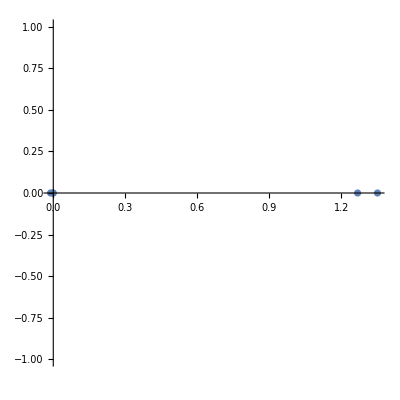

```mathematica
frequency[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
```

```mathematica
(*
(*data needed to check if the energy is negative*)
ϵ= 3/1000; spinSuppressFac = ϵ^(1/2);    c = 1/spinSuppressFac   ;
 μ =m1  m2 /(m1+m2); M=m1+m2;
Q1=(2+3 m2/(2 m1));Q2=(2+3 m1/(2 m2));
Linit=Cross[Rinit, Pinit];
SeffLN=(Q1 S1init+ Q2 S2init).Linit;
En=μ ((Pinit.Pinit)/(2 μ^2)-(G M)/Norm[Rinit]) + (G ϵ SeffLN)/(Norm[Rinit])^3 //Simplify*)
```